```mathematica
SymbolReplace[sym_,edge_]:=Block[{s},
s=SymbolToSets[sym];
s=Map[Sort[Flatten[(#/.edge[[1]]->{edge[[1]],edge[[2]]})]]&,s];
SetsToSymbol[s]
]
```

```mathematica
FinerSymbols[syms_]:=Sort[DeleteDuplicates[Map[SetsToSymbol,Flatten[Map[FindFiner,Map[SymbolToSets,syms]],1]]],CompareSymbols]
```

```mathematica
CoarserSymbols[syms_]:=Sort[DeleteDuplicates[Map[SetsToSymbol,Flatten[Map[FindCoarser,Map[SymbolToSets,syms]],1]]],CompareSymbols]
```

```mathematica
ExamineFormula2[g_]:=Block[{
all=FindFullFormula4[g], 
rest(*=DeleteDuplicates[Flatten[Table[Map[SymbolReplace[#,e]&,Map[SetsToSymbol,Flatten[Map[FindFiner,Map[SymbolToSets[FindFullFormula4[EdgeContract[g,e]]]]]]]],{e,EdgeList[g]}]]]*),
rest5,
rest4,
filtered,
all5,all4
}
,
rest=Table[Map[SymbolReplace[#,e]&,FindFullFormula4[EdgeContract[g,e]]],{e,EdgeList[g]}];
rest=Flatten[rest];
Print[rest];
(*rest=FinerSymbols[rest];*)
rest=Sort[DeleteDuplicates[rest]];
rest5=Select[FinerSymbols[rest],SymbolLevel[#]==5&];
rest4=Select[CoarserSymbols[rest5],SymbolLevel[#]==4&];
filtered=Select[rest4,MemberQ[rest,#]||MemberQ[all,#]&];
all5=FinerSymbols[all];
all4=CoarserSymbols[all5];
Print[Map[If[MemberQ[rest,#],Style[#,Darker[Green]],If[MemberQ[all,#],Style[#,Red],#]]&,all4]];
Map[If[MemberQ[rest,#]&&MemberQ[all,#],Style[#,Darker[Green]],If[MemberQ[all,#],Style[#,Red],If[MemberQ[rest,#],Style[#,Blue],#]]]&,filtered]
]
```

```mathematica
CoarserSymbols[FinerSymbols[{v1x23x4x567}]]
```

{v12x3x4x567,v13x2x4x567,v14x2x3x567,v1567x2x3x4,v1x23x4x567,v1x24x3x567,v1x2567x3x4,v1x2x34x567,v1x2x3567x4,v1x2x3x4567,v123x4x5x67,v14x23x5x67,v15x23x4x67,v167x23x4x5,v1x234x5x67,v1x235x4x67,v1x2367x4x5,v1x23x45x67,v1x23x467x5,v123x4x56x7,v14x23x56x7,v156x23x4x7,v17x23x4x56,v1x234x56x7,v1x2356x4x7,v1x237x4x56,v1x23x456x7,v1x23x47x56,v123x4x57x6,v14x23x57x6,v157x23x4x6,v16x23x4x57,v1x234x57x6,v1x2357x4x6,v1x236x4x57,v1x23x457x6,v1x23x46x57}

```mathematica
JacobsThalGraph[2]//EdgeCount
```

12

```mathematica
IsRefinement[SymbolToSets[v12x34x5x6],SymbolToSets[v1x2x34x5x6]]
```

True

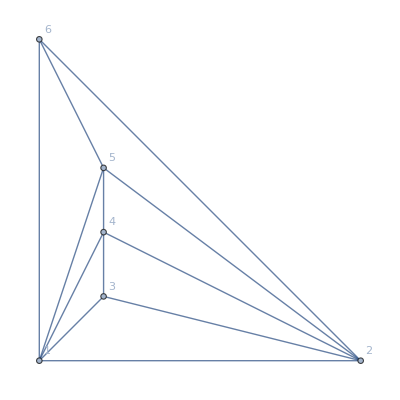

```mathematica
MinimalGraph[5]
```

```mathematica
Table[ExamineFormula2[MinimalGraph[k]]//Length,{k,5,12}]//Differences//Differences
```

{4,8,16,32,64,128}

```mathematica
ExamineFormula2[JacobsThalGraph[3]]
```

{v126x3x4x57,v126x34x5x7,v12x34x57x6,v16x2x4x57,v1x26x4x57,v14x26x3x57,v16x24x3x57,v17x2x34x6,v17x26x3x4,v1x26x34x7,v1x25x34x6,v16x25x3x4,v16x2x34x5,v16x25x3x4,v17x26x3x4,v17x26x3x4,v1x25x34x7,v17x2x34x5,v17x25x3x4,v17x25x3x4,v17x25x3x4,v1x25x34x6,v16x2x34x5,v16x25x3x4,v16x25x3x4}

{v12x34x57x6,v134x2x57x6,v157x2x34x6,v16x2x34x57,v1x234x57x6,v1x257x34x6,v1x26x34x57,v1x2x3457x6,v1x2x346x57,v1x2x34x567,v126x3x4x57,v13x26x4x57,v14x26x3x57,v157x26x3x4,v1x236x4x57,v1x246x3x57,v1x2567x3x4,v1x26x357x4,v1x26x3x457,v126x34x5x7,v134x26x5x7,v15x26x34x7,v17x26x34x5,v1x2346x5x7,v1x256x34x7,v1x267x34x5,v1x26x345x7,v1x26x347x5,v136x2x4x57,v146x2x3x57,v1567x2x3x4,v16x23x4x57,v16x24x3x57,v16x257x3x4,v16x2x357x4,v16x2x3x457,v1346x2x5x7,v156x2x34x7,v167x2x34x5,v16x234x5x7,v16x25x34x7,v16x27x34x5,v16x2x345x7,v16x2x347x5,v125x34x6x7,v134x25x6x7,v17x25x34x6,v1x2345x6x7,v1x25x346x7,v1x25x347x6,v1x25x34x67,v1256x3x4x7,v136x25x4x7,v146x25x3x7,v167x25x3x4,v16x235x4x7,v16x245x3x7,v16x25x37x4,v16x25x3x47,v127x34x5x6,v1347x2x5x6,v17x234x5x6,v17x2x345x6,v17x2x346x5,v17x2x34x56,v1267x3x4x5,v137x26x4x5,v147x26x3x5,v17x236x4x5,v17x246x3x5,v17x256x3x4,v17x26x35x4,v17x26x3x45,v1257x3x4x6,v137x25x4x6,v147x25x3x6,v17x235x4x6,v17x245x3x6,v17x25x36x4,v17x25x3x46}

{v126x34x5x7,v17x26x34x5,v1x26x34x57,v12x34x57x6,v16x25x34x7,v16x2x34x57,v126x3x4x57,v14x26x3x57,v16x24x3x57,v16x25x3x4,v1x25x34x6,v16x2x34x5,v16x2x4x57,v1x26x4x57,v17x25x3x4,v1x25x34x7,v17x2x34x5,v17x26x3x4,v1x26x34x7,v17x2x34x6}

```mathematica
FinerSymbols[{v1x2x34x57x6,v1x26x3x4x57,v1x26x34x5x7,v16x2x3x4x57,v16x2x34x5x7,v1x25x34x6x7,v16x25x3x4x7,v17x2x34x5x6,v17x26x3x4x5,v17x25x3x4x6}]
```

{v1x2x3x4x57x6,v1x2x34x5x6x7,v1x26x3x4x5x7,v16x2x3x4x5x7,v1x25x3x4x6x7,v17x2x3x4x5x6}

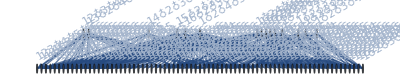

```mathematica
FormulaGraphReverse2[{v12x35x4x6,v135x2x4x6,v14x2x35x6,v16x2x35x4,v1x235x4x6,v1x24x35x6,v1x26x35x4,v1x2x345x6,v1x2x356x4,v1x2x35x46,v123x4x5x6,v124x3x5x6,v125x3x4x6,v126x3x4x5,v12x34x5x6,v12x36x4x5,v12x3x45x6,v12x3x46x5,v12x3x4x56,v136x2x4x5,v14x2x36x5,v15x2x36x4,v1x236x4x5,v1x24x36x5,v1x25x36x4,v1x2x346x5,v1x2x36x45,v13x2x46x5,v146x2x3x5,v15x2x3x46,v1x23x46x5,v1x246x3x5,v1x25x3x46,v1x2x3x456,v134x2x5x6,v13x24x5x6,v13x25x4x6,v13x26x4x5,v13x2x45x6,v13x2x4x56,v145x2x3x6,v14x23x5x6,v14x25x3x6,v14x26x3x5,v14x2x3x56,v156x2x3x4,v15x23x4x6,v15x24x3x6,v15x26x3x4,v15x2x34x6,v16x23x4x5,v16x24x3x5,v16x25x3x4,v16x2x34x5,v16x2x3x45,v1x234x5x6,v1x245x3x6,v1x24x3x56,v1x256x3x4,v1x25x34x6,v1x26x34x5,v1x26x3x45,v1x2x34x56,v1x23x4x56,v1x23x45x6,v12x4x5x6,v14x2x5x6,v15x2x4x6,v16x2x4x5,v1x24x5x6,v1x25x4x6,v1x26x4x5,v1x2x45x6,v1x2x46x5,v1x2x4x56,v12x35x4x6,v12x36x4x5,v12x3x46x5,v13x2x46x5,v14x2x35x6,v14x2x36x5,v15x2x36x4,v15x2x3x46,v16x2x35x4,v1x24x35x6,v1x24x36x5,v1x25x36x4,v1x25x3x46,v1x26x35x4,v1x2x346x5,v1x2x356x4,v1x2x36x45,v1x2x46x5,v1x2x35x4x6,v12x3x4x5x6,v1x2x36x4x5,v1x2x3x46x5,v13x2x4x5x6,v14x2x3x5x6,v15x2x3x4x6,v16x2x3x4x5,v1x24x3x5x6,v1x25x3x4x6,v1x26x3x4x5,v1x2x34x5x6,v1x2x3x4x56,v1x2x3x45x6,v1x2x4x5x6}]
```